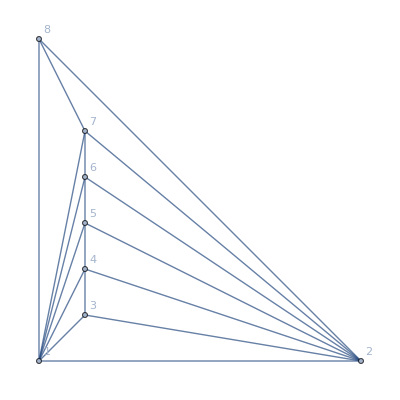

```mathematica
g=MinimalGraph[7]
```

```mathematica
e=MissingEdges[g]
```

{{v1x2x357x468,3<->6},{v1x2x357x468,3<->8},{v1x2x357x468,5<->8},{v1x2x357x468,4<->7}}

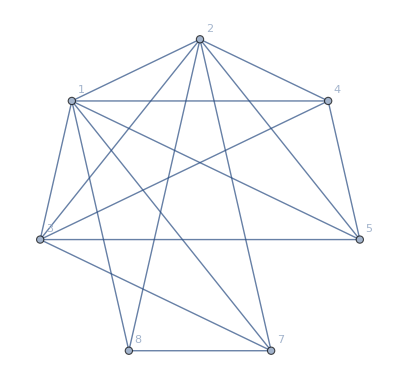

```mathematica
h=VertexContract[g,{3,6}, GraphLayout->"CircularEmbedding"]
```

```mathematica
FindClique[h]
```

{{1,2,4,5,3}}

```mathematica
Roots[ChromaticPolynomial[h,x]==0,x]
```

x==0||x==1||x==2||x==3||x==3||x==3||x==4

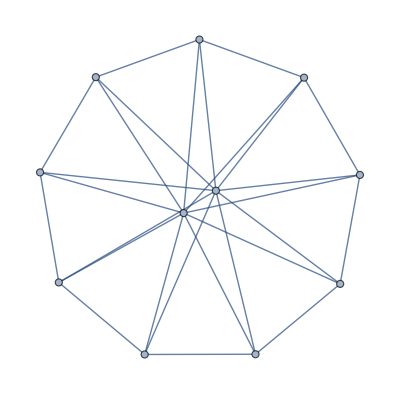

```mathematica
g=JacobsThalGraph[7]
```

```mathematica
e=MissingEdges[g]
```

{{v1x268ax34x579b,1<->6},{v1x268ax34x579b,1<->8},{v1x268ax34x579b,1<->10},{v1x268ax34x579b,1<->7},{v1x268ax34x579b,1<->9},{v1x268ax34x579b,1<->11},{v1x268ax34x579b,2<->5},{v1x268ax34x579b,2<->7},{v1x268ax34x579b,2<->9},{v1x268ax34x579b,6<->9},{v1x268ax34x579b,6<->11},{v1x268ax34x579b,5<->8},{v1x268ax34x579b,8<->11},{v1x268ax34x579b,5<->10},{v1x268ax34x579b,7<->10},{v1ax268x34x579b,1<->6},{v1ax268x34x579b,1<->8},{v1ax268x34x579b,2<->10},{v1ax268x34x579b,6<->10},{v1ax268x34x579b,8<->10},{v1ax268x34x579b,1<->7},{v1ax268x34x579b,1<->9},{v1ax268x34x579b,1<->11},{v1ax268x34x579b,5<->10},{v1ax268x34x579b,7<->10},{v1ax268x34x579b,2<->5},{v1ax268x34x579b,2<->7},{v1ax268x34x579b,2<->9},{v1ax268x34x579b,6<->9},{v1ax268x34x579b,6<->11},{v1ax268x34x579b,5<->8},{v1ax268x34x579b,8<->11},{v1ax2579x34x68b,1<->7},{v1ax2579x34x68b,1<->9},{v1ax2579x34x68b,2<->10},{v1ax2579x34x68b,5<->10},{v1ax2579x34x68b,7<->10},{v1ax2579x34x68b,1<->6},{v1ax2579x34x68b,1<->8},{v1ax2579x34x68b,1<->11},{v1ax2579x34x68b,6<->10},{v1ax2579x34x68b,8<->10},{v1ax2579x34x68b,2<->6},{v1ax2579x34x68b,2<->8},{v1ax2579x34x68b,5<->8},{v1ax2579x34x68b,5<->11},{v1ax2579x34x68b,7<->11},{v1ax2579x34x68b,6<->9},{v1ax2579x34x68b,9<->11},{v19x268ax34x57b,1<->6},{v19x268ax34x57b,1<->8},{v19x268ax34x57b,1<->10},{v19x268ax34x57b,2<->9},{v19x268ax34x57b,6<->9},{v19x268ax34x57b,1<->7},{v19x268ax34x57b,1<->11},{v19x268ax34x57b,5<->9},{v19x268ax34x57b,7<->9},{v19x268ax34x57b,9<->11},{v19x268ax34x57b,2<->5},{v19x268ax34x57b,2<->7},{v19x268ax34x57b,6<->11},{v19x268ax34x57b,5<->8},{v19x268ax34x57b,8<->11},{v19x268ax34x57b,5<->10},{v19x268ax34x57b,7<->10},{v19x257ax34x68b,1<->7},{v19x257ax34x68b,1<->10},{v19x257ax34x68b,2<->9},{v19x257ax34x68b,5<->9},{v19x257ax34x68b,7<->9},{v19x257ax34x68b,1<->6},{v19x257ax34x68b,1<->8},{v19x257ax34x68b,1<->11},{v19x257ax34x68b,6<->9},{v19x257ax34x68b,9<->11},{v19x257ax34x68b,2<->6},{v19x257ax34x68b,2<->8},{v19x257ax34x68b,5<->8},{v19x257ax34x68b,5<->11},{v19x257ax34x68b,7<->11},{v19x257ax34x68b,6<->10},{v19x257ax34x68b,8<->10},{v18ax269x34x57b,1<->6},{v18ax269x34x57b,1<->9},{v18ax269x34x57b,2<->8},{v18ax269x34x57b,6<->8},{v18ax269x34x57b,2<->10},{v18ax269x34x57b,6<->10},{v18ax269x34x57b,1<->7},{v18ax269x34x57b,1<->11},{v18ax269x34x57b,5<->8},{v18ax269x34x57b,8<->11},{v18ax269x34x57b,5<->10},{v18ax269x34x57b,7<->10},{v18ax269x34x57b,2<->5},{v18ax269x34x57b,2<->7},{v18ax269x34x57b,6<->11},{v18ax269x34x57b,5<->9},{v18ax269x34x57b,7<->9},{v18ax269x34x57b,9<->11},{v18x26ax34x579b,1<->6},{v18x26ax34x579b,1<->10},{v18x26ax34x579b,2<->8},{v18x26ax34x579b,6<->8},{v18x26ax34x579b,8<->10},{v18x26ax34x579b,1<->7},{v18x26ax34x579b,1<->9},{v18x26ax34x579b,1<->11},{v18x26ax34x579b,5<->8},{v18x26ax34x579b,8<->11},{v18x26ax34x579b,2<->5},{v18x26ax34x579b,2<->7},{v18x26ax34x579b,2<->9},{v18x26ax34x579b,6<->9},{v18x26ax34x579b,6<->11},{v18x26ax34x579b,5<->10},{v18x26ax34x579b,7<->10},{v18ax26x34x579b,1<->6},{v18ax26x34x579b,2<->8},{v18ax26x34x579b,6<->8},{v18ax26x34x579b,2<->10},{v18ax26x34x579b,6<->10},{v18ax26x34x579b,1<->7},{v18ax26x34x579b,1<->9},{v18ax26x34x579b,1<->11},{v18ax26x34x579b,5<->8},{v18ax26x34x579b,8<->11},{v18ax26x34x579b,5<->10},{v18ax26x34x579b,7<->10},{v18ax26x34x579b,2<->5},{v18ax26x34x579b,2<->7},{v18ax26x34x579b,2<->9},{v18ax26x34x579b,6<->9},{v18ax26x34x579b,6<->11},{v18ax257x34x69b,1<->7},{v18ax257x34x69b,2<->8},{v18ax257x34x69b,5<->8},{v18ax257x34x69b,2<->10},{v18ax257x34x69b,5<->10},{v18ax257x34x69b,7<->10},{v18ax257x34x69b,1<->6},{v18ax257x34x69b,1<->9},{v18ax257x34x69b,1<->11},{v18ax257x34x69b,6<->8},{v18ax257x34x69b,8<->11},{v18ax257x34x69b,6<->10},{v18ax257x34x69b,2<->6},{v18ax257x34x69b,2<->9},{v18ax257x34x69b,5<->9},{v18ax257x34x69b,5<->11},{v18ax257x34x69b,7<->9},{v18ax257x34x69b,7<->11},{v18x257ax34x69b,1<->7},{v18x257ax34x69b,1<->10},{v18x257ax34x69b,2<->8},{v18x257ax34x69b,5<->8},{v18x257ax34x69b,8<->10},{v18x257ax34x69b,1<->6},{v18x257ax34x69b,1<->9},{v18x257ax34x69b,1<->11},{v18x257ax34x69b,6<->8},{v18x257ax34x69b,8<->11},{v18x257ax34x69b,2<->6},{v18x257ax34x69b,2<->9},{v18x257ax34x69b,5<->9},{v18x257ax34x69b,5<->11},{v18x257ax34x69b,7<->9},{v18x257ax34x69b,7<->11},{v18x257ax34x69b,6<->10},{v18ax2579x34x6b,1<->7},{v18ax2579x34x6b,1<->9},{v18ax2579x34x6b,2<->8},{v18ax2579x34x6b,5<->8},{v18ax2579x34x6b,2<->10},{v18ax2579x34x6b,5<->10},{v18ax2579x34x6b,7<->10},{v18ax2579x34x6b,1<->6},{v18ax2579x34x6b,1<->11},{v18ax2579x34x6b,6<->8},{v18ax2579x34x6b,8<->11},{v18ax2579x34x6b,6<->10},{v18ax2579x34x6b,2<->6},{v18ax2579x34x6b,5<->11},{v18ax2579x34x6b,7<->11},{v18ax2579x34x6b,6<->9},{v18ax2579x34x6b,9<->11},{v17ax269x34x58b,1<->6},{v17ax269x34x58b,1<->9},{v17ax269x34x58b,2<->7},{v17ax269x34x58b,7<->9},{v17ax269x34x58b,2<->10},{v17ax269x34x58b,6<->10},{v17ax269x34x58b,1<->8},{v17ax269x34x58b,1<->11},{v17ax269x34x58b,5<->7},{v17ax269x34x58b,7<->11},{v17ax269x34x58b,5<->10},{v17ax269x34x58b,8<->10},{v17ax269x34x58b,2<->5},{v17ax269x34x58b,2<->8},{v17ax269x34x58b,6<->8},{v17ax269x34x58b,6<->11},{v17ax269x34x58b,5<->9},{v17ax269x34x58b,9<->11},{v179x26ax34x58b,1<->6},{v179x26ax34x58b,1<->10},{v179x26ax34x58b,2<->7},{v179x26ax34x58b,7<->10},{v179x26ax34x58b,2<->9},{v179x26ax34x58b,6<->9},{v179x26ax34x58b,1<->8},{v179x26ax34x58b,1<->11},{v179x26ax34x58b,5<->7},{v179x26ax34x58b,7<->11},{v179x26ax34x58b,5<->9},{v179x26ax34x58b,9<->11},{v179x26ax34x58b,2<->5},{v179x26ax34x58b,2<->8},{v179x26ax34x58b,6<->8},{v179x26ax34x58b,6<->11},{v179x26ax34x58b,5<->10},{v179x26ax34x58b,8<->10},{v17ax268x34x59b,1<->6},{v17ax268x34x59b,1<->8},{v17ax268x34x59b,2<->7},{v17ax268x34x59b,2<->10},{v17ax268x34x59b,6<->10},{v17ax268x34x59b,8<->10},{v17ax268x34x59b,1<->9},{v17ax268x34x59b,1<->11},{v17ax268x34x59b,5<->7},{v17ax268x34x59b,7<->9},{v17ax268x34x59b,7<->11},{v17ax268x34x59b,5<->10},{v17ax268x34x59b,2<->5},{v17ax268x34x59b,2<->9},{v17ax268x34x59b,6<->9},{v17ax268x34x59b,6<->11},{v17ax268x34x59b,5<->8},{v17ax268x34x59b,8<->11},{v17x268ax34x59b,1<->6},{v17x268ax34x59b,1<->8},{v17x268ax34x59b,1<->10},{v17x268ax34x59b,2<->7},{v17x268ax34x59b,7<->10},{v17x268ax34x59b,1<->9},{v17x268ax34x59b,1<->11},{v17x268ax34x59b,5<->7},{v17x268ax34x59b,7<->9},{v17x268ax34x59b,7<->11},{v17x268ax34x59b,2<->5},{v17x268ax34x59b,2<->9},{v17x268ax34x59b,6<->9},{v17x268ax34x59b,6<->11},{v17x268ax34x59b,5<->8},{v17x268ax34x59b,8<->11},{v17x268ax34x59b,5<->10},{v179x268ax34x5b,1<->6},{v179x268ax34x5b,1<->8},{v179x268ax34x5b,1<->10},{v179x268ax34x5b,2<->7},{v179x268ax34x5b,7<->10},{v179x268ax34x5b,2<->9},{v179x268ax34x5b,6<->9},{v179x268ax34x5b,1<->11},{v179x268ax34x5b,5<->7},{v179x268ax34x5b,7<->11},{v179x268ax34x5b,5<->9},{v179x268ax34x5b,9<->11},{v179x268ax34x5b,2<->5},{v179x268ax34x5b,6<->11},{v179x268ax34x5b,5<->8},{v179x268ax34x5b,8<->11},{v179x268ax34x5b,5<->10},{v17ax259x34x68b,1<->9},{v17ax259x34x68b,2<->7},{v17ax259x34x68b,5<->7},{v17ax259x34x68b,7<->9},{v17ax259x34x68b,2<->10},{v17ax259x34x68b,5<->10},{v17ax259x34x68b,1<->6},{v17ax259x34x68b,1<->8},{v17ax259x34x68b,1<->11},{v17ax259x34x68b,7<->11},{v17ax259x34x68b,6<->10},{v17ax259x34x68b,8<->10},{v17ax259x34x68b,2<->6},{v17ax259x34x68b,2<->8},{v17ax259x34x68b,5<->8},{v17ax259x34x68b,5<->11},{v17ax259x34x68b,6<->9},{v17ax259x34x68b,9<->11},{v179x25ax34x68b,1<->10},{v179x25ax34x68b,2<->7},{v179x25ax34x68b,5<->7},{v179x25ax34x68b,7<->10},{v179x25ax34x68b,2<->9},{v179x25ax34x68b,5<->9},{v179x25ax34x68b,1<->6},{v179x25ax34x68b,1<->8},{v179x25ax34x68b,1<->11},{v179x25ax34x68b,7<->11},{v179x25ax34x68b,6<->9},{v179x25ax34x68b,9<->11},{v179x25ax34x68b,2<->6},{v179x25ax34x68b,2<->8},{v179x25ax34x68b,5<->8},{v179x25ax34x68b,5<->11},{v179x25ax34x68b,6<->10},{v179x25ax34x68b,8<->10},{v17ax258x34x69b,1<->8},{v17ax258x34x69b,2<->7},{v17ax258x34x69b,5<->7},{v17ax258x34x69b,2<->10},{v17ax258x34x69b,5<->10},{v17ax258x34x69b,8<->10},{v17ax258x34x69b,1<->6},{v17ax258x34x69b,1<->9},{v17ax258x34x69b,1<->11},{v17ax258x34x69b,7<->9},{v17ax258x34x69b,7<->11},{v17ax258x34x69b,6<->10},{v17ax258x34x69b,2<->6},{v17ax258x34x69b,2<->9},{v17ax258x34x69b,5<->9},{v17ax258x34x69b,5<->11},{v17ax258x34x69b,6<->8},{v17ax258x34x69b,8<->11},{v17x258ax34x69b,1<->8},{v17x258ax34x69b,1<->10},{v17x258ax34x69b,2<->7},{v17x258ax34x69b,5<->7},{v17x258ax34x69b,7<->10},{v17x258ax34x69b,1<->6},{v17x258ax34x69b,1<->9},{v17x258ax34x69b,1<->11},{v17x258ax34x69b,7<->9},{v17x258ax34x69b,7<->11},{v17x258ax34x69b,2<->6},{v17x258ax34x69b,2<->9},{v17x258ax34x69b,5<->9},{v17x258ax34x69b,5<->11},{v17x258ax34x69b,6<->8},{v17x258ax34x69b,8<->11},{v17x258ax34x69b,6<->10},{v179x258ax34x6b,1<->8},{v179x258ax34x6b,1<->10},{v179x258ax34x6b,2<->7},{v179x258ax34x6b,5<->7},{v179x258ax34x6b,7<->10},{v179x258ax34x6b,2<->9},{v179x258ax34x6b,5<->9},{v179x258ax34x6b,1<->6},{v179x258ax34x6b,1<->11},{v179x258ax34x6b,7<->11},{v179x258ax34x6b,6<->9},{v179x258ax34x6b,9<->11},{v179x258ax34x6b,2<->6},{v179x258ax34x6b,5<->11},{v179x258ax34x6b,6<->8},{v179x258ax34x6b,8<->11},{v179x258ax34x6b,6<->10},{v168ax2x34x579b,2<->6},{v168ax2x34x579b,2<->8},{v168ax2x34x579b,2<->10},{v168ax2x34x579b,1<->7},{v168ax2x34x579b,1<->9},{v168ax2x34x579b,1<->11},{v168ax2x34x579b,6<->9},{v168ax2x34x579b,6<->11},{v168ax2x34x579b,5<->8},{v168ax2x34x579b,8<->11},{v168ax2x34x579b,5<->10},{v168ax2x34x579b,7<->10},{v168ax2x34x579b,2<->5},{v168ax2x34x579b,2<->7},{v168ax2x34x579b,2<->9},{v168x2ax34x579b,1<->10},{v168x2ax34x579b,2<->6},{v168x2ax34x579b,6<->10},{v168x2ax34x579b,2<->8},{v168x2ax34x579b,8<->10},{v168x2ax34x579b,1<->7},{v168x2ax34x579b,1<->9},{v168x2ax34x579b,1<->11},{v168x2ax34x579b,6<->9},{v168x2ax34x579b,6<->11},{v168x2ax34x579b,5<->8},{v168x2ax34x579b,8<->11},{v168x2ax34x579b,2<->5},{v168x2ax34x579b,2<->7},{v168x2ax34x579b,2<->9},{v168x2ax34x579b,5<->10},{v168x2ax34x579b,7<->10},{v168ax29x34x57b,1<->9},{v168ax29x34x57b,2<->6},{v168ax29x34x57b,6<->9},{v168ax29x34x57b,2<->8},{v168ax29x34x57b,2<->10},{v168ax29x34x57b,1<->7},{v168ax29x34x57b,1<->11},{v168ax29x34x57b,6<->11},{v168ax29x34x57b,5<->8},{v168ax29x34x57b,8<->11},{v168ax29x34x57b,5<->10},{v168ax29x34x57b,7<->10},{v168ax29x34x57b,2<->5},{v168ax29x34x57b,2<->7},{v168ax29x34x57b,5<->9},{v168ax29x34x57b,7<->9},{v168ax29x34x57b,9<->11},{v169x28ax34x57b,1<->8},{v169x28ax34x57b,1<->10},{v169x28ax34x57b,2<->6},{v169x28ax34x57b,6<->8},{v169x28ax34x57b,6<->10},{v169x28ax34x57b,2<->9},{v169x28ax34x57b,1<->7},{v169x28ax34x57b,1<->11},{v169x28ax34x57b,6<->11},{v169x28ax34x57b,5<->9},{v169x28ax34x57b,7<->9},{v169x28ax34x57b,9<->11},{v169x28ax34x57b,2<->5},{v169x28ax34x57b,2<->7},{v169x28ax34x57b,5<->8},{v169x28ax34x57b,8<->11},{v169x28ax34x57b,5<->10},{v169x28ax34x57b,7<->10},{v16x28ax34x579b,1<->8},{v16x28ax34x579b,1<->10},{v16x28ax34x579b,2<->6},{v16x28ax34x579b,6<->8},{v16x28ax34x579b,6<->10},{v16x28ax34x579b,1<->7},{v16x28ax34x579b,1<->9},{v16x28ax34x579b,1<->11},{v16x28ax34x579b,6<->9},{v16x28ax34x579b,6<->11},{v16x28ax34x579b,2<->5},{v16x28ax34x579b,2<->7},{v16x28ax34x579b,2<->9},{v16x28ax34x579b,5<->8},{v16x28ax34x579b,8<->11},{v16x28ax34x579b,5<->10},{v16x28ax34x579b,7<->10},{v16ax28x34x579b,1<->8},{v16ax28x34x579b,2<->6},{v16ax28x34x579b,6<->8},{v16ax28x34x579b,2<->10},{v16ax28x34x579b,8<->10},{v16ax28x34x579b,1<->7},{v16ax28x34x579b,1<->9},{v16ax28x34x579b,1<->11},{v16ax28x34x579b,6<->9},{v16ax28x34x579b,6<->11},{v16ax28x34x579b,5<->10},{v16ax28x34x579b,7<->10},{v16ax28x34x579b,2<->5},{v16ax28x34x579b,2<->7},{v16ax28x34x579b,2<->9},{v16ax28x34x579b,5<->8},{v16ax28x34x579b,8<->11},{v16ax279x34x58b,1<->7},{v16ax279x34x58b,1<->9},{v16ax279x34x58b,2<->6},{v16ax279x34x58b,6<->9},{v16ax279x34x58b,2<->10},{v16ax279x34x58b,7<->10},{v16ax279x34x58b,1<->8},{v16ax279x34x58b,1<->11},{v16ax279x34x58b,6<->8},{v16ax279x34x58b,6<->11},{v16ax279x34x58b,5<->10},{v16ax279x34x58b,8<->10},{v16ax279x34x58b,2<->5},{v16ax279x34x58b,2<->8},{v16ax279x34x58b,5<->7},{v16ax279x34x58b,7<->11},{v16ax279x34x58b,5<->9},{v16ax279x34x58b,9<->11},{v169x27ax34x58b,1<->7},{v169x27ax34x58b,1<->10},{v169x27ax34x58b,2<->6},{v169x27ax34x58b,6<->10},{v169x27ax34x58b,2<->9},{v169x27ax34x58b,7<->9},{v169x27ax34x58b,1<->8},{v169x27ax34x58b,1<->11},{v169x27ax34x58b,6<->8},{v169x27ax34x58b,6<->11},{v169x27ax34x58b,5<->9},{v169x27ax34x58b,9<->11},{v169x27ax34x58b,2<->5},{v169x27ax34x58b,2<->8},{v169x27ax34x58b,5<->7},{v169x27ax34x58b,7<->11},{v169x27ax34x58b,5<->10},{v169x27ax34x58b,8<->10},{v168x27ax34x59b,1<->7},{v168x27ax34x59b,1<->10},{v168x27ax34x59b,2<->6},{v168x27ax34x59b,6<->10},{v168x27ax34x59b,2<->8},{v168x27ax34x59b,8<->10},{v168x27ax34x59b,1<->9},{v168x27ax34x59b,1<->11},{v168x27ax34x59b,6<->9},{v168x27ax34x59b,6<->11},{v168x27ax34x59b,5<->8},{v168x27ax34x59b,8<->11},{v168x27ax34x59b,2<->5},{v168x27ax34x59b,2<->9},{v168x27ax34x59b,5<->7},{v168x27ax34x59b,7<->9},{v168x27ax34x59b,7<->11},{v168x27ax34x59b,5<->10},{v168ax27x34x59b,1<->7},{v168ax27x34x59b,2<->6},{v168ax27x34x59b,2<->8},{v168ax27x34x59b,2<->10},{v168ax27x34x59b,7<->10},{v168ax27x34x59b,1<->9},{v168ax27x34x59b,1<->11},{v168ax27x34x59b,6<->9},{v168ax27x34x59b,6<->11},{v168ax27x34x59b,5<->8},{v168ax27x34x59b,8<->11},{v168ax27x34x59b,5<->10},{v168ax27x34x59b,2<->5},{v168ax27x34x59b,2<->9},{v168ax27x34x59b,5<->7},{v168ax27x34x59b,7<->9},{v168ax27x34x59b,7<->11},{v168ax279x34x5b,1<->7},{v168ax279x34x5b,1<->9},{v168ax279x34x5b,2<->6},{v168ax279x34x5b,6<->9},{v168ax279x34x5b,2<->8},{v168ax279x34x5b,2<->10},{v168ax279x34x5b,7<->10},{v168ax279x34x5b,1<->11},{v168ax279x34x5b,6<->11},{v168ax279x34x5b,5<->8},{v168ax279x34x5b,8<->11},{v168ax279x34x5b,5<->10},{v168ax279x34x5b,2<->5},{v168ax279x34x5b,5<->7},{v168ax279x34x5b,7<->11},{v168ax279x34x5b,5<->9},{v168ax279x34x5b,9<->11},{v168ax2579x34xb,1<->7},{v168ax2579x34xb,1<->9},{v168ax2579x34xb,2<->6},{v168ax2579x34xb,6<->9},{v168ax2579x34xb,2<->8},{v168ax2579x34xb,5<->8},{v168ax2579x34xb,2<->10},{v168ax2579x34xb,5<->10},{v168ax2579x34xb,7<->10},{v168ax2579x34xb,1<->11},{v168ax2579x34xb,6<->11},{v168ax2579x34xb,8<->11},{v168ax2579x34xb,5<->11},{v168ax2579x34xb,7<->11},{v168ax2579x34xb,9<->11},{v168ax257x34x9b,1<->7},{v168ax257x34x9b,2<->6},{v168ax257x34x9b,2<->8},{v168ax257x34x9b,5<->8},{v168ax257x34x9b,2<->10},{v168ax257x34x9b,5<->10},{v168ax257x34x9b,7<->10},{v168ax257x34x9b,1<->9},{v168ax257x34x9b,1<->11},{v168ax257x34x9b,6<->9},{v168ax257x34x9b,6<->11},{v168ax257x34x9b,8<->11},{v168ax257x34x9b,2<->9},{v168ax257x34x9b,5<->9},{v168ax257x34x9b,5<->11},{v168ax257x34x9b,7<->9},{v168ax257x34x9b,7<->11},{v168x257ax34x9b,1<->7},{v168x257ax34x9b,1<->10},{v168x257ax34x9b,2<->6},{v168x257ax34x9b,6<->10},{v168x257ax34x9b,2<->8},{v168x257ax34x9b,5<->8},{v168x257ax34x9b,8<->10},{v168x257ax34x9b,1<->9},{v168x257ax34x9b,1<->11},{v168x257ax34x9b,6<->9},{v168x257ax34x9b,6<->11},{v168x257ax34x9b,8<->11},{v168x257ax34x9b,2<->9},{v168x257ax34x9b,5<->9},{v168x257ax34x9b,5<->11},{v168x257ax34x9b,7<->9},{v168x257ax34x9b,7<->11},{v169x257ax34x8b,1<->7},{v169x257ax34x8b,1<->10},{v169x257ax34x8b,2<->6},{v169x257ax34x8b,6<->10},{v169x257ax34x8b,2<->9},{v169x257ax34x8b,5<->9},{v169x257ax34x8b,7<->9},{v169x257ax34x8b,1<->8},{v169x257ax34x8b,1<->11},{v169x257ax34x8b,6<->8},{v169x257ax34x8b,6<->11},{v169x257ax34x8b,9<->11},{v169x257ax34x8b,2<->8},{v169x257ax34x8b,5<->8},{v169x257ax34x8b,5<->11},{v169x257ax34x8b,7<->11},{v169x257ax34x8b,8<->10},{v16ax2579x34x8b,1<->7},{v16ax2579x34x8b,1<->9},{v16ax2579x34x8b,2<->6},{v16ax2579x34x8b,6<->9},{v16ax2579x34x8b,2<->10},{v16ax2579x34x8b,5<->10},{v16ax2579x34x8b,7<->10},{v16ax2579x34x8b,1<->8},{v16ax2579x34x8b,1<->11},{v16ax2579x34x8b,6<->8},{v16ax2579x34x8b,6<->11},{v16ax2579x34x8b,8<->10},{v16ax2579x34x8b,2<->8},{v16ax2579x34x8b,5<->8},{v16ax2579x34x8b,5<->11},{v16ax2579x34x8b,7<->11},{v16ax2579x34x8b,9<->11},{v16ax258x34x79b,1<->8},{v16ax258x34x79b,2<->6},{v16ax258x34x79b,6<->8},{v16ax258x34x79b,2<->10},{v16ax258x34x79b,5<->10},{v16ax258x34x79b,8<->10},{v16ax258x34x79b,1<->7},{v16ax258x34x79b,1<->9},{v16ax258x34x79b,1<->11},{v16ax258x34x79b,6<->9},{v16ax258x34x79b,6<->11},{v16ax258x34x79b,7<->10},{v16ax258x34x79b,2<->7},{v16ax258x34x79b,2<->9},{v16ax258x34x79b,5<->7},{v16ax258x34x79b,5<->9},{v16ax258x34x79b,5<->11},{v16ax258x34x79b,8<->11},{v168x25ax34x79b,1<->10},{v168x25ax34x79b,2<->6},{v168x25ax34x79b,6<->10},{v168x25ax34x79b,2<->8},{v168x25ax34x79b,5<->8},{v168x25ax34x79b,8<->10},{v168x25ax34x79b,1<->7},{v168x25ax34x79b,1<->9},{v168x25ax34x79b,1<->11},{v168x25ax34x79b,6<->9},{v168x25ax34x79b,6<->11},{v168x25ax34x79b,8<->11},{v168x25ax34x79b,2<->7},{v168x25ax34x79b,2<->9},{v168x25ax34x79b,5<->7},{v168x25ax34x79b,5<->9},{v168x25ax34x79b,5<->11},{v168x25ax34x79b,7<->10},{v16x258ax34x79b,1<->8},{v16x258ax34x79b,1<->10},{v16x258ax34x79b,2<->6},{v16x258ax34x79b,6<->8},{v16x258ax34x79b,6<->10},{v16x258ax34x79b,1<->7},{v16x258ax34x79b,1<->9},{v16x258ax34x79b,1<->11},{v16x258ax34x79b,6<->9},{v16x258ax34x79b,6<->11},{v16x258ax34x79b,2<->7},{v16x258ax34x79b,2<->9},{v16x258ax34x79b,5<->7},{v16x258ax34x79b,5<->9},{v16x258ax34x79b,5<->11},{v16x258ax34x79b,8<->11},{v16x258ax34x79b,7<->10},{v168ax25x34x79b,2<->6},{v168ax25x34x79b,2<->8},{v168ax25x34x79b,5<->8},{v168ax25x34x79b,2<->10},{v168ax25x34x79b,5<->10},{v168ax25x34x79b,1<->7},{v168ax25x34x79b,1<->9},{v168ax25x34x79b,1<->11},{v168ax25x34x79b,6<->9},{v168ax25x34x79b,6<->11},{v168ax25x34x79b,8<->11},{v168ax25x34x79b,7<->10},{v168ax25x34x79b,2<->7},{v168ax25x34x79b,2<->9},{v168ax25x34x79b,5<->7},{v168ax25x34x79b,5<->9},{v168ax25x34x79b,5<->11},{v168ax259x34x7b,1<->9},{v168ax259x34x7b,2<->6},{v168ax259x34x7b,6<->9},{v168ax259x34x7b,2<->8},{v168ax259x34x7b,5<->8},{v168ax259x34x7b,2<->10},{v168ax259x34x7b,5<->10},{v168ax259x34x7b,1<->7},{v168ax259x34x7b,1<->11},{v168ax259x34x7b,6<->11},{v168ax259x34x7b,8<->11},{v168ax259x34x7b,7<->10},{v168ax259x34x7b,2<->7},{v168ax259x34x7b,5<->7},{v168ax259x34x7b,5<->11},{v168ax259x34x7b,7<->9},{v168ax259x34x7b,9<->11},{v169x258ax34x7b,1<->8},{v169x258ax34x7b,1<->10},{v169x258ax34x7b,2<->6},{v169x258ax34x7b,6<->8},{v169x258ax34x7b,6<->10},{v169x258ax34x7b,2<->9},{v169x258ax34x7b,5<->9},{v169x258ax34x7b,1<->7},{v169x258ax34x7b,1<->11},{v169x258ax34x7b,6<->11},{v169x258ax34x7b,7<->9},{v169x258ax34x7b,9<->11},{v169x258ax34x7b,2<->7},{v169x258ax34x7b,5<->7},{v169x258ax34x7b,5<->11},{v169x258ax34x7b,8<->11},{v169x258ax34x7b,7<->10},{v168bx2ax34x579,1<->10},{v168bx2ax34x579,2<->6},{v168bx2ax34x579,6<->10},{v168bx2ax34x579,2<->8},{v168bx2ax34x579,8<->10},{v168bx2ax34x579,1<->7},{v168bx2ax34x579,1<->9},{v168bx2ax34x579,6<->9},{v168bx2ax34x579,5<->8},{v168bx2ax34x579,5<->11},{v168bx2ax34x579,7<->11},{v168bx2ax34x579,9<->11},{v168bx2ax34x579,2<->5},{v168bx2ax34x579,2<->7},{v168bx2ax34x579,2<->9},{v168bx2ax34x579,5<->10},{v168bx2ax34x579,7<->10},{v168bx29x34x57a,1<->9},{v168bx29x34x57a,2<->6},{v168bx29x34x57a,6<->9},{v168bx29x34x57a,2<->8},{v168bx29x34x57a,9<->11},{v168bx29x34x57a,1<->7},{v168bx29x34x57a,1<->10},{v168bx29x34x57a,6<->10},{v168bx29x34x57a,5<->8},{v168bx29x34x57a,8<->10},{v168bx29x34x57a,5<->11},{v168bx29x34x57a,7<->11},{v168bx29x34x57a,2<->5},{v168bx29x34x57a,2<->7},{v168bx29x34x57a,2<->10},{v168bx29x34x57a,5<->9},{v168bx29x34x57a,7<->9},{v16bx28ax34x579,1<->8},{v16bx28ax34x579,1<->10},{v16bx28ax34x579,2<->6},{v16bx28ax34x579,6<->8},{v16bx28ax34x579,6<->10},{v16bx28ax34x579,8<->11},{v16bx28ax34x579,1<->7},{v16bx28ax34x579,1<->9},{v16bx28ax34x579,6<->9},{v16bx28ax34x579,5<->11},{v16bx28ax34x579,7<->11},{v16bx28ax34x579,9<->11},{v16bx28ax34x579,2<->5},{v16bx28ax34x579,2<->7},{v16bx28ax34x579,2<->9},{v16bx28ax34x579,5<->8},{v16bx28ax34x579,5<->10},{v16bx28ax34x579,7<->10},{v169bx28x34x57a,1<->8},{v169bx28x34x57a,2<->6},{v169bx28x34x57a,6<->8},{v169bx28x34x57a,2<->9},{v169bx28x34x57a,8<->11},{v169bx28x34x57a,1<->7},{v169bx28x34x57a,1<->10},{v169bx28x34x57a,6<->10},{v169bx28x34x57a,5<->9},{v169bx28x34x57a,7<->9},{v169bx28x34x57a,5<->11},{v169bx28x34x57a,7<->11},{v169bx28x34x57a,2<->5},{v169bx28x34x57a,2<->7},{v169bx28x34x57a,2<->10},{v169bx28x34x57a,5<->8},{v169bx28x34x57a,8<->10},{v169bx28ax34x57,1<->8},{v169bx28ax34x57,1<->10},{v169bx28ax34x57,2<->6},{v169bx28ax34x57,6<->8},{v169bx28ax34x57,6<->10},{v169bx28ax34x57,2<->9},{v169bx28ax34x57,8<->11},{v169bx28ax34x57,1<->7},{v169bx28ax34x57,5<->9},{v169bx28ax34x57,7<->9},{v169bx28ax34x57,5<->11},{v169bx28ax34x57,7<->11},{v169bx28ax34x57,2<->5},{v169bx28ax34x57,2<->7},{v169bx28ax34x57,5<->8},{v169bx28ax34x57,5<->10},{v169bx28ax34x57,7<->10},{v168bx279x34x5a,1<->7},{v168bx279x34x5a,1<->9},{v168bx279x34x5a,2<->6},{v168bx279x34x5a,6<->9},{v168bx279x34x5a,2<->8},{v168bx279x34x5a,7<->11},{v168bx279x34x5a,9<->11},{v168bx279x34x5a,1<->10},{v168bx279x34x5a,6<->10},{v168bx279x34x5a,5<->8},{v168bx279x34x5a,8<->10},{v168bx279x34x5a,5<->11},{v168bx279x34x5a,2<->5},{v168bx279x34x5a,2<->10},{v168bx279x34x5a,5<->7},{v168bx279x34x5a,7<->10},{v168bx279x34x5a,5<->9},{v168bx27ax34x59,1<->7},{v168bx27ax34x59,1<->10},{v168bx27ax34x59,2<->6},{v168bx27ax34x59,6<->10},{v168bx27ax34x59,2<->8},{v168bx27ax34x59,8<->10},{v168bx27ax34x59,7<->11},{v168bx27ax34x59,1<->9},{v168bx27ax34x59,6<->9},{v168bx27ax34x59,5<->8},{v168bx27ax34x59,5<->11},{v168bx27ax34x59,9<->11},{v168bx27ax34x59,2<->5},{v168bx27ax34x59,2<->9},{v168bx27ax34x59,5<->7},{v168bx27ax34x59,7<->9},{v168bx27ax34x59,5<->10},{v16bx279x34x58a,1<->7},{v16bx279x34x58a,1<->9},{v16bx279x34x58a,2<->6},{v16bx279x34x58a,6<->9},{v16bx279x34x58a,7<->11},{v16bx279x34x58a,9<->11},{v16bx279x34x58a,1<->8},{v16bx279x34x58a,1<->10},{v16bx279x34x58a,6<->8},{v16bx279x34x58a,6<->10},{v16bx279x34x58a,5<->11},{v16bx279x34x58a,8<->11},{v16bx279x34x58a,2<->5},{v16bx279x34x58a,2<->8},{v16bx279x34x58a,2<->10},{v16bx279x34x58a,5<->7},{v16bx279x34x58a,7<->10},{v16bx279x34x58a,5<->9},{v169bx27x34x58a,1<->7},{v169bx27x34x58a,2<->6},{v169bx27x34x58a,2<->9},{v169bx27x34x58a,7<->9},{v169bx27x34x58a,7<->11},{v169bx27x34x58a,1<->8},{v169bx27x34x58a,1<->10},{v169bx27x34x58a,6<->8},{v169bx27x34x58a,6<->10},{v169bx27x34x58a,5<->9},{v169bx27x34x58a,5<->11},{v169bx27x34x58a,8<->11},{v169bx27x34x58a,2<->5},{v169bx27x34x58a,2<->8},{v169bx27x34x58a,2<->10},{v169bx27x34x58a,5<->7},{v169bx27x34x58a,7<->10},{v169bx27ax34x58,1<->7},{v169bx27ax34x58,1<->10},{v169bx27ax34x58,2<->6},{v169bx27ax34x58,6<->10},{v169bx27ax34x58,2<->9},{v169bx27ax34x58,7<->9},{v169bx27ax34x58,7<->11},{v169bx27ax34x58,1<->8},{v169bx27ax34x58,6<->8},{v169bx27ax34x58,5<->9},{v169bx27ax34x58,5<->11},{v169bx27ax34x58,8<->11},{v169bx27ax34x58,2<->5},{v169bx27ax34x58,2<->8},{v169bx27ax34x58,5<->7},{v169bx27ax34x58,5<->10},{v169bx27ax34x58,8<->10},{v179bx268ax34x5,1<->6},{v179bx268ax34x5,1<->8},{v179bx268ax34x5,1<->10},{v179bx268ax34x5,2<->7},{v179bx268ax34x5,7<->10},{v179bx268ax34x5,2<->9},{v179bx268ax34x5,6<->9},{v179bx268ax34x5,6<->11},{v179bx268ax34x5,8<->11},{v179bx268ax34x5,5<->7},{v179bx268ax34x5,5<->9},{v179bx268ax34x5,5<->11},{v179bx268ax34x5,2<->5},{v179bx268ax34x5,5<->8},{v179bx268ax34x5,5<->10},{v179bx268x34x5a,1<->6},{v179bx268x34x5a,1<->8},{v179bx268x34x5a,2<->7},{v179bx268x34x5a,2<->9},{v179bx268x34x5a,6<->9},{v179bx268x34x5a,6<->11},{v179bx268x34x5a,8<->11},{v179bx268x34x5a,1<->10},{v179bx268x34x5a,5<->7},{v179bx268x34x5a,7<->10},{v179bx268x34x5a,5<->9},{v179bx268x34x5a,5<->11},{v179bx268x34x5a,2<->5},{v179bx268x34x5a,2<->10},{v179bx268x34x5a,6<->10},{v179bx268x34x5a,5<->8},{v179bx268x34x5a,8<->10},{v17bx268ax34x59,1<->6},{v17bx268ax34x59,1<->8},{v17bx268ax34x59,1<->10},{v17bx268ax34x59,2<->7},{v17bx268ax34x59,7<->10},{v17bx268ax34x59,6<->11},{v17bx268ax34x59,8<->11},{v17bx268ax34x59,1<->9},{v17bx268ax34x59,5<->7},{v17bx268ax34x59,7<->9},{v17bx268ax34x59,5<->11},{v17bx268ax34x59,9<->11},{v17bx268ax34x59,2<->5},{v17bx268ax34x59,2<->9},{v17bx268ax34x59,6<->9},{v17bx268ax34x59,5<->8},{v17bx268ax34x59,5<->10},{v17bx269x34x58a,1<->6},{v17bx269x34x58a,1<->9},{v17bx269x34x58a,2<->7},{v17bx269x34x58a,7<->9},{v17bx269x34x58a,6<->11},{v17bx269x34x58a,9<->11},{v17bx269x34x58a,1<->8},{v17bx269x34x58a,1<->10},{v17bx269x34x58a,5<->7},{v17bx269x34x58a,7<->10},{v17bx269x34x58a,5<->11},{v17bx269x34x58a,8<->11},{v17bx269x34x58a,2<->5},{v17bx269x34x58a,2<->8},{v17bx269x34x58a,2<->10},{v17bx269x34x58a,6<->8},{v17bx269x34x58a,6<->10},{v17bx269x34x58a,5<->9},{v179bx26x34x58a,1<->6},{v179bx26x34x58a,2<->7},{v179bx26x34x58a,2<->9},{v179bx26x34x58a,6<->9},{v179bx26x34x58a,6<->11},{v179bx26x34x58a,1<->8},{v179bx26x34x58a,1<->10},{v179bx26x34x58a,5<->7},{v179bx26x34x58a,7<->10},{v179bx26x34x58a,5<->9},{v179bx26x34x58a,5<->11},{v179bx26x34x58a,8<->11},{v179bx26x34x58a,2<->5},{v179bx26x34x58a,2<->8},{v179bx26x34x58a,2<->10},{v179bx26x34x58a,6<->8},{v179bx26x34x58a,6<->10},{v179bx26ax34x58,1<->6},{v179bx26ax34x58,1<->10},{v179bx26ax34x58,2<->7},{v179bx26ax34x58,7<->10},{v179bx26ax34x58,2<->9},{v179bx26ax34x58,6<->9},{v179bx26ax34x58,6<->11},{v179bx26ax34x58,1<->8},{v179bx26ax34x58,5<->7},{v179bx26ax34x58,5<->9},{v179bx26ax34x58,5<->11},{v179bx26ax34x58,8<->11},{v179bx26ax34x58,2<->5},{v179bx26ax34x58,2<->8},{v179bx26ax34x58,6<->8},{v179bx26ax34x58,5<->10},{v179bx26ax34x58,8<->10},{v19bx268x34x57a,1<->6},{v19bx268x34x57a,1<->8},{v19bx268x34x57a,2<->9},{v19bx268x34x57a,6<->9},{v19bx268x34x57a,6<->11},{v19bx268x34x57a,8<->11},{v19bx268x34x57a,1<->7},{v19bx268x34x57a,1<->10},{v19bx268x34x57a,5<->9},{v19bx268x34x57a,7<->9},{v19bx268x34x57a,5<->11},{v19bx268x34x57a,7<->11},{v19bx268x34x57a,2<->5},{v19bx268x34x57a,2<->7},{v19bx268x34x57a,2<->10},{v19bx268x34x57a,6<->10},{v19bx268x34x57a,5<->8},{v19bx268x34x57a,8<->10},{v18bx26ax34x579,1<->6},{v18bx26ax34x579,1<->10},{v18bx26ax34x579,2<->8},{v18bx26ax34x579,6<->8},{v18bx26ax34x579,8<->10},{v18bx26ax34x579,6<->11},{v18bx26ax34x579,1<->7},{v18bx26ax34x579,1<->9},{v18bx26ax34x579,5<->8},{v18bx26ax34x579,5<->11},{v18bx26ax34x579,7<->11},{v18bx26ax34x579,9<->11},{v18bx26ax34x579,2<->5},{v18bx26ax34x579,2<->7},{v18bx26ax34x579,2<->9},{v18bx26ax34x579,6<->9},{v18bx26ax34x579,5<->10},{v18bx26ax34x579,7<->10},{v18bx269x34x57a,1<->6},{v18bx269x34x57a,1<->9},{v18bx269x34x57a,2<->8},{v18bx269x34x57a,6<->8},{v18bx269x34x57a,6<->11},{v18bx269x34x57a,9<->11},{v18bx269x34x57a,1<->7},{v18bx269x34x57a,1<->10},{v18bx269x34x57a,5<->8},{v18bx269x34x57a,8<->10},{v18bx269x34x57a,5<->11},{v18bx269x34x57a,7<->11},{v18bx269x34x57a,2<->5},{v18bx269x34x57a,2<->7},{v18bx269x34x57a,2<->10},{v18bx269x34x57a,6<->10},{v18bx269x34x57a,5<->9},{v18bx269x34x57a,7<->9},{v1bx268ax34x579,1<->6},{v1bx268ax34x579,1<->8},{v1bx268ax34x579,1<->10},{v1bx268ax34x579,6<->11},{v1bx268ax34x579,8<->11},{v1bx268ax34x579,1<->7},{v1bx268ax34x579,1<->9},{v1bx268ax34x579,5<->11},{v1bx268ax34x579,7<->11},{v1bx268ax34x579,9<->11},{v1bx268ax34x579,2<->5},{v1bx268ax34x579,2<->7},{v1bx268ax34x579,2<->9},{v1bx268ax34x579,6<->9},{v1bx268ax34x579,5<->8},{v1bx268ax34x579,5<->10},{v1bx268ax34x579,7<->10},{v19bx268ax34x57,1<->6},{v19bx268ax34x57,1<->8},{v19bx268ax34x57,1<->10},{v19bx268ax34x57,2<->9},{v19bx268ax34x57,6<->9},{v19bx268ax34x57,6<->11},{v19bx268ax34x57,8<->11},{v19bx268ax34x57,1<->7},{v19bx268ax34x57,5<->9},{v19bx268ax34x57,7<->9},{v19bx268ax34x57,5<->11},{v19bx268ax34x57,7<->11},{v19bx268ax34x57,2<->5},{v19bx268ax34x57,2<->7},{v19bx268ax34x57,5<->8},{v19bx268ax34x57,5<->10},{v19bx268ax34x57,7<->10},{v179bx258ax34x6,1<->8},{v179bx258ax34x6,1<->10},{v179bx258ax34x6,2<->7},{v179bx258ax34x6,5<->7},{v179bx258ax34x6,7<->10},{v179bx258ax34x6,2<->9},{v179bx258ax34x6,5<->9},{v179bx258ax34x6,5<->11},{v179bx258ax34x6,8<->11},{v179bx258ax34x6,1<->6},{v179bx258ax34x6,6<->9},{v179bx258ax34x6,6<->11},{v179bx258ax34x6,2<->6},{v179bx258ax34x6,6<->8},{v179bx258ax34x6,6<->10},{v16bx258ax34x79,1<->8},{v16bx258ax34x79,1<->10},{v16bx258ax34x79,2<->6},{v16bx258ax34x79,6<->8},{v16bx258ax34x79,6<->10},{v16bx258ax34x79,5<->11},{v16bx258ax34x79,8<->11},{v16bx258ax34x79,1<->7},{v16bx258ax34x79,1<->9},{v16bx258ax34x79,6<->9},{v16bx258ax34x79,7<->11},{v16bx258ax34x79,9<->11},{v16bx258ax34x79,2<->7},{v16bx258ax34x79,2<->9},{v16bx258ax34x79,5<->7},{v16bx258ax34x79,5<->9},{v16bx258ax34x79,7<->10},{v16bx2579x34x8a,1<->7},{v16bx2579x34x8a,1<->9},{v16bx2579x34x8a,2<->6},{v16bx2579x34x8a,6<->9},{v16bx2579x34x8a,5<->11},{v16bx2579x34x8a,7<->11},{v16bx2579x34x8a,9<->11},{v16bx2579x34x8a,1<->8},{v16bx2579x34x8a,1<->10},{v16bx2579x34x8a,6<->8},{v16bx2579x34x8a,6<->10},{v16bx2579x34x8a,8<->11},{v16bx2579x34x8a,2<->8},{v16bx2579x34x8a,2<->10},{v16bx2579x34x8a,5<->8},{v16bx2579x34x8a,5<->10},{v16bx2579x34x8a,7<->10},{v179bx258x34x6a,1<->8},{v179bx258x34x6a,2<->7},{v179bx258x34x6a,5<->7},{v179bx258x34x6a,2<->9},{v179bx258x34x6a,5<->9},{v179bx258x34x6a,5<->11},{v179bx258x34x6a,8<->11},{v179bx258x34x6a,1<->6},{v179bx258x34x6a,1<->10},{v179bx258x34x6a,7<->10},{v179bx258x34x6a,6<->9},{v179bx258x34x6a,6<->11},{v179bx258x34x6a,2<->6},{v179bx258x34x6a,2<->10},{v179bx258x34x6a,5<->10},{v179bx258x34x6a,6<->8},{v179bx258x34x6a,8<->10},{v18bx2579x34x6a,1<->7},{v18bx2579x34x6a,1<->9},{v18bx2579x34x6a,2<->8},{v18bx2579x34x6a,5<->8},{v18bx2579x34x6a,5<->11},{v18bx2579x34x6a,7<->11},{v18bx2579x34x6a,9<->11},{v18bx2579x34x6a,1<->6},{v18bx2579x34x6a,1<->10},{v18bx2579x34x6a,6<->8},{v18bx2579x34x6a,8<->10},{v18bx2579x34x6a,6<->11},{v18bx2579x34x6a,2<->6},{v18bx2579x34x6a,2<->10},{v18bx2579x34x6a,5<->10},{v18bx2579x34x6a,7<->10},{v18bx2579x34x6a,6<->9},{v169bx258ax34x7,1<->8},{v169bx258ax34x7,1<->10},{v169bx258ax34x7,2<->6},{v169bx258ax34x7,6<->8},{v169bx258ax34x7,6<->10},{v169bx258ax34x7,2<->9},{v169bx258ax34x7,5<->9},{v169bx258ax34x7,5<->11},{v169bx258ax34x7,8<->11},{v169bx258ax34x7,1<->7},{v169bx258ax34x7,7<->9},{v169bx258ax34x7,7<->11},{v169bx258ax34x7,2<->7},{v169bx258ax34x7,5<->7},{v169bx258ax34x7,7<->10},{v169bx257x34x8a,1<->7},{v169bx257x34x8a,2<->6},{v169bx257x34x8a,2<->9},{v169bx257x34x8a,5<->9},{v169bx257x34x8a,7<->9},{v169bx257x34x8a,5<->11},{v169bx257x34x8a,7<->11},{v169bx257x34x8a,1<->8},{v169bx257x34x8a,1<->10},{v169bx257x34x8a,6<->8},{v169bx257x34x8a,6<->10},{v169bx257x34x8a,8<->11},{v169bx257x34x8a,2<->8},{v169bx257x34x8a,2<->10},{v169bx257x34x8a,5<->8},{v169bx257x34x8a,5<->10},{v169bx257x34x8a,7<->10},{v17bx258ax34x69,1<->8},{v17bx258ax34x69,1<->10},{v17bx258ax34x69,2<->7},{v17bx258ax34x69,5<->7},{v17bx258ax34x69,7<->10},{v17bx258ax34x69,5<->11},{v17bx258ax34x69,8<->11},{v17bx258ax34x69,1<->6},{v17bx258ax34x69,1<->9},{v17bx258ax34x69,7<->9},{v17bx258ax34x69,6<->11},{v17bx258ax34x69,9<->11},{v17bx258ax34x69,2<->6},{v17bx258ax34x69,2<->9},{v17bx258ax34x69,5<->9},{v17bx258ax34x69,6<->8},{v17bx258ax34x69,6<->10},{v169bx257ax34x8,1<->7},{v169bx257ax34x8,1<->10},{v169bx257ax34x8,2<->6},{v169bx257ax34x8,6<->10},{v169bx257ax34x8,2<->9},{v169bx257ax34x8,5<->9},{v169bx257ax34x8,7<->9},{v169bx257ax34x8,5<->11},{v169bx257ax34x8,7<->11},{v169bx257ax34x8,1<->8},{v169bx257ax34x8,6<->8},{v169bx257ax34x8,8<->11},{v169bx257ax34x8,2<->8},{v169bx257ax34x8,5<->8},{v169bx257ax34x8,8<->10},{v169bx258x34x7a,1<->8},{v169bx258x34x7a,2<->6},{v169bx258x34x7a,6<->8},{v169bx258x34x7a,2<->9},{v169bx258x34x7a,5<->9},{v169bx258x34x7a,5<->11},{v169bx258x34x7a,8<->11},{v169bx258x34x7a,1<->7},{v169bx258x34x7a,1<->10},{v169bx258x34x7a,6<->10},{v169bx258x34x7a,7<->9},{v169bx258x34x7a,7<->11},{v169bx258x34x7a,2<->7},{v169bx258x34x7a,2<->10},{v169bx258x34x7a,5<->7},{v169bx258x34x7a,5<->10},{v169bx258x34x7a,8<->10},{v18bx257ax34x69,1<->7},{v18bx257ax34x69,1<->10},{v18bx257ax34x69,2<->8},{v18bx257ax34x69,5<->8},{v18bx257ax34x69,8<->10},{v18bx257ax34x69,5<->11},{v18bx257ax34x69,7<->11},{v18bx257ax34x69,1<->6},{v18bx257ax34x69,1<->9},{v18bx257ax34x69,6<->8},{v18bx257ax34x69,6<->11},{v18bx257ax34x69,9<->11},{v18bx257ax34x69,2<->6},{v18bx257ax34x69,2<->9},{v18bx257ax34x69,5<->9},{v18bx257ax34x69,7<->9},{v18bx257ax34x69,6<->10},{v19bx257x34x68a,1<->7},{v19bx257x34x68a,2<->9},{v19bx257x34x68a,5<->9},{v19bx257x34x68a,7<->9},{v19bx257x34x68a,5<->11},{v19bx257x34x68a,7<->11},{v19bx257x34x68a,1<->6},{v19bx257x34x68a,1<->8},{v19bx257x34x68a,1<->10},{v19bx257x34x68a,6<->9},{v19bx257x34x68a,6<->11},{v19bx257x34x68a,8<->11},{v19bx257x34x68a,2<->6},{v19bx257x34x68a,2<->8},{v19bx257x34x68a,2<->10},{v19bx257x34x68a,5<->8},{v19bx257x34x68a,5<->10},{v19bx257x34x68a,7<->10},{v17bx259x34x68a,1<->9},{v17bx259x34x68a,2<->7},{v17bx259x34x68a,5<->7},{v17bx259x34x68a,7<->9},{v17bx259x34x68a,5<->11},{v17bx259x34x68a,9<->11},{v17bx259x34x68a,1<->6},{v17bx259x34x68a,1<->8},{v17bx259x34x68a,1<->10},{v17bx259x34x68a,7<->10},{v17bx259x34x68a,6<->11},{v17bx259x34x68a,8<->11},{v17bx259x34x68a,2<->6},{v17bx259x34x68a,2<->8},{v17bx259x34x68a,2<->10},{v17bx259x34x68a,5<->8},{v17bx259x34x68a,5<->10},{v17bx259x34x68a,6<->9},{v168bx257ax34x9,1<->7},{v168bx257ax34x9,1<->10},{v168bx257ax34x9,2<->6},{v168bx257ax34x9,6<->10},{v168bx257ax34x9,2<->8},{v168bx257ax34x9,5<->8},{v168bx257ax34x9,8<->10},{v168bx257ax34x9,5<->11},{v168bx257ax34x9,7<->11},{v168bx257ax34x9,1<->9},{v168bx257ax34x9,6<->9},{v168bx257ax34x9,9<->11},{v168bx257ax34x9,2<->9},{v168bx257ax34x9,5<->9},{v168bx257ax34x9,7<->9},{v168bx259x34x7a,1<->9},{v168bx259x34x7a,2<->6},{v168bx259x34x7a,6<->9},{v168bx259x34x7a,2<->8},{v168bx259x34x7a,5<->8},{v168bx259x34x7a,5<->11},{v168bx259x34x7a,9<->11},{v168bx259x34x7a,1<->7},{v168bx259x34x7a,1<->10},{v168bx259x34x7a,6<->10},{v168bx259x34x7a,8<->10},{v168bx259x34x7a,7<->11},{v168bx259x34x7a,2<->7},{v168bx259x34x7a,2<->10},{v168bx259x34x7a,5<->7},{v168bx259x34x7a,5<->10},{v168bx259x34x7a,7<->9},{v19bx257ax34x68,1<->7},{v19bx257ax34x68,1<->10},{v19bx257ax34x68,2<->9},{v19bx257ax34x68,5<->9},{v19bx257ax34x68,7<->9},{v19bx257ax34x68,5<->11},{v19bx257ax34x68,7<->11},{v19bx257ax34x68,1<->6},{v19bx257ax34x68,1<->8},{v19bx257ax34x68,6<->9},{v19bx257ax34x68,6<->11},{v19bx257ax34x68,8<->11},{v19bx257ax34x68,2<->6},{v19bx257ax34x68,2<->8},{v19bx257ax34x68,5<->8},{v19bx257ax34x68,6<->10},{v19bx257ax34x68,8<->10},{v168bx2579x34xa,1<->7},{v168bx2579x34xa,1<->9},{v168bx2579x34xa,2<->6},{v168bx2579x34xa,6<->9},{v168bx2579x34xa,2<->8},{v168bx2579x34xa,5<->8},{v168bx2579x34xa,5<->11},{v168bx2579x34xa,7<->11},{v168bx2579x34xa,9<->11},{v168bx2579x34xa,1<->10},{v168bx2579x34xa,6<->10},{v168bx2579x34xa,8<->10},{v168bx2579x34xa,2<->10},{v168bx2579x34xa,5<->10},{v168bx2579x34xa,7<->10},{v1bx2579x34x68a,1<->7},{v1bx2579x34x68a,1<->9},{v1bx2579x34x68a,5<->11},{v1bx2579x34x68a,7<->11},{v1bx2579x34x68a,9<->11},{v1bx2579x34x68a,1<->6},{v1bx2579x34x68a,1<->8},{v1bx2579x34x68a,1<->10},{v1bx2579x34x68a,6<->11},{v1bx2579x34x68a,8<->11},{v1bx2579x34x68a,2<->6},{v1bx2579x34x68a,2<->8},{v1bx2579x34x68a,2<->10},{v1bx2579x34x68a,5<->8},{v1bx2579x34x68a,5<->10},{v1bx2579x34x68a,7<->10},{v1bx2579x34x68a,6<->9},{v179bx25x34x68a,2<->7},{v179bx25x34x68a,5<->7},{v179bx25x34x68a,2<->9},{v179bx25x34x68a,5<->9},{v179bx25x34x68a,5<->11},{v179bx25x34x68a,1<->6},{v179bx25x34x68a,1<->8},{v179bx25x34x68a,1<->10},{v179bx25x34x68a,7<->10},{v179bx25x34x68a,6<->9},{v179bx25x34x68a,6<->11},{v179bx25x34x68a,8<->11},{v179bx25x34x68a,2<->6},{v179bx25x34x68a,2<->8},{v179bx25x34x68a,2<->10},{v179bx25x34x68a,5<->8},{v179bx25x34x68a,5<->10},{v179bx25ax34x68,1<->10},{v179bx25ax34x68,2<->7},{v179bx25ax34x68,5<->7},{v179bx25ax34x68,7<->10},{v179bx25ax34x68,2<->9},{v179bx25ax34x68,5<->9},{v179bx25ax34x68,5<->11},{v179bx25ax34x68,1<->6},{v179bx25ax34x68,1<->8},{v179bx25ax34x68,6<->9},{v179bx25ax34x68,6<->11},{v179bx25ax34x68,8<->11},{v179bx25ax34x68,2<->6},{v179bx25ax34x68,2<->8},{v179bx25ax34x68,5<->8},{v179bx25ax34x68,6<->10},{v179bx25ax34x68,8<->10},{v168bx25ax34x79,1<->10},{v168bx25ax34x79,2<->6},{v168bx25ax34x79,6<->10},{v168bx25ax34x79,2<->8},{v168bx25ax34x79,5<->8},{v168bx25ax34x79,8<->10},{v168bx25ax34x79,5<->11},{v168bx25ax34x79,1<->7},{v168bx25ax34x79,1<->9},{v168bx25ax34x79,6<->9},{v168bx25ax34x79,7<->11},{v168bx25ax34x79,9<->11},{v168bx25ax34x79,2<->7},{v168bx25ax34x79,2<->9},{v168bx25ax34x79,5<->7},{v168bx25ax34x79,5<->9},{v168bx25ax34x79,7<->10}}

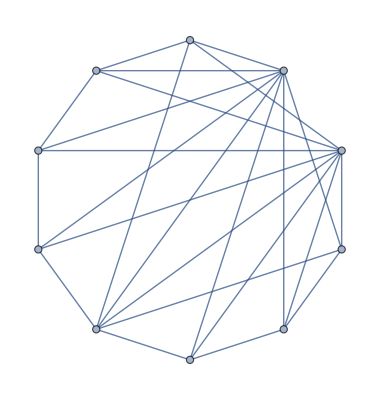

```mathematica
h=VertexContract[g,{7,11}, GraphLayout->"CircularEmbedding"]
```

```mathematica
FindClique[h]
{{1,2,4,5,3}}

x==0||x==1||x==2||x==3||x==3||x==3||x==4
```

{{1,2,3}}

{{1,2,4,5,3}}

x==0||x==Root2.72-0.396 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,1]2.7245299901614977||x==Root2.72+0.396 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,2]2.7245299901614977||x==Root2.76-1.05 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,3]2.763948331129732||x==Root2.76+1.05 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,4]2.763948331129732||x==Root4.01-2.53 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,5]4.011521678708787||x==Root4.01+2.53 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,6]4.011521678708787||x==1||x==2||x==3

x==0||x==1||x==2||x==3||x==3||x==3||x==4

```mathematica
Roots[ChromaticPolynomial[h,x]==0,x]
```

x==0||x==Root2.72-0.396 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,1]2.7245299901614977||x==Root2.72+0.396 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,2]2.7245299901614977||x==Root2.76-1.05 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,3]2.763948331129732||x==Root2.76+1.05 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,4]2.763948331129732||x==Root4.01-2.53 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,5]4.011521678708787||x==Root4.01+2.53 ⅈRoot[1490-2545 #1+1829 #1^2-709 #1^3+157 #1^4-19 #1^5+#1^6&,6]4.011521678708787||x==1||x==2||x==3

```mathematica
Onky[set_,diff_]:=Select[set,#≠diff&]
```

```mathematica
RemoveSym[s_,v_]:=SetsToSymbol[Map[Onky[#,v]&,SymbolToSets[s]]]
```

```mathematica
RemoveSym[v168x2ax34x579b,11]
```

v168x2ax34x579

```mathematica
s1=Map[RemoveSym[#,11]&,FindFullFormula[g]];Length[s1]
```

6850

```mathematica
s2=FindFullFormula[h];Length[s2]
```

1180

```mathematica
s1//Length
```

85

```mathematica
s2//Length
```

30

```mathematica
Intersection[s1,s2]//Length
```

1180